```mathematica
U[x_]:=Subscript[U, 0]*Piecewise[{{Mod[x,l+L]/l,Mod[x,l+L]<l},{-Mod[x,l+L]/L+(l+L)/L,Mod[x,l+L]≥l}}]
```

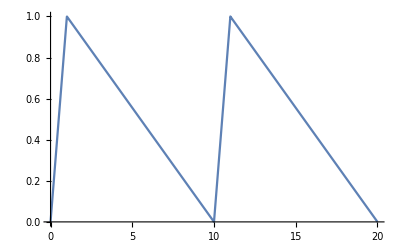

```mathematica
Plot[U[x]/.{Subscript[U, 0]->1,l->1,L->9},{x,0,20}]
```

```mathematica
Subscript[Z, h] = Integrate[Exp[-k*y^2/(2*Subscript[T, h])],{y,-∞,∞},Assumptions->{k>0,Subscript[T, h]>0}]
```

√(2 π) √(T_h/k)

```mathematica
ph=1/Subscript[Z, h]*Exp[-k*y^2/(2*Subscript[T, h])]
```

(ⅇ^(-(k y^2)/(2 T_h)))/(√(2 π) √(T_h/k))

```mathematica
Subscript[Z, c] = Integrate[Exp[-U[x]/Subscript[T, c]],{x,0,l+L},Assumptions->{l>0,L>0,Subscript[T, c]>0}]
```

(ⅇ^(-U_0/T_c) (-1+ⅇ^(U_0/T_c)) (l+L) T_c)/U_0

```mathematica
pc = Exp[-U[x]/Subscript[T, c]]/Subscript[Z, c]
```

(ⅇ^(U_0/T_c-((Piecewise[{{Mod[x,l+L]/l, Mod[x,l+L]<l}, {(l+L)/L-Mod[x,l+L]/L, Mod[x,l+L]≥l}, {0, True}}]) U_0)/T_c) U_0)/((-1+ⅇ^(U_0/T_c)) (l+L) T_c)

```mathematica
Integrate[y^2*ph,{y,-∞,∞},Assumptions->{k>0,Subscript[T, h]>0}]
```

T_h/k

```mathematica
N[Log[6]-Log[2]-Log[3]]
```

0.

```mathematica
N[Log[1]+Log[2]+Log[3]]
```

1.79176